```mathematica
(* define distribution computed in part a *)
𝒟=ProbabilityDistribution[3 t^2,{t,0,1}];
```

```mathematica
PDF[𝒟,t]
```

Piecewise[{{3 t^2, 0<t<1}, {0, True}}]

```mathematica
(* generate & store n=10^5 random variables from 𝒟 *)
data =RandomVariate[𝒟,10^5];
```

```mathematica
(* compute and print variance of 𝒟 with 4 sig. digits *)
N[Variance[𝒟],4]
```

0.0375

```mathematica
(* compute and print mean of 𝒟 with 4 sig. digits *)
N[Mean[𝒟],4]
```

0.75

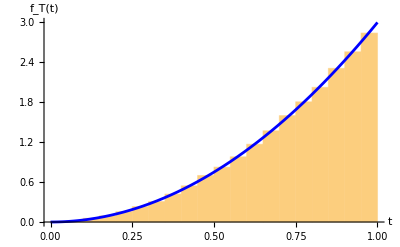

```mathematica
(* plot histogram of random samples with overaly of PDF computed earlier *)
Show[Histogram[data,Automatic,"PDF", AxesLabel->{t,"f_T(t)"}],Plot[PDF[𝒟,t],{t,0,1},PlotStyle->Blue]]
```